## 1) Towards a Theory of Bulk Orchestration

#### Objective:

Develop a foundational theoretical framework that allows one to greatly simplify accurate molecular-scale (and larger) simulations in biology

#### Background:

In chemistry, one can do molecular dynamics to simulate the behavior of every single molecule in a system.  But for many chemical purposes, it’s sufficient to use what amounts to a probabilistic model in which all that matters is the overall concentration of molecules of different types.  For biology this approach is often tried, but is much less likely to work, because biological systems don’t consist of randomly mixed molecules.  Instead, a major takeaway from molecular biology over the past few decades has been that there’s some kind of “bulk orchestration” of molecular processes: molecules are not moving around randomly, but are carefully channeled through a network of interactions, associated with particular membranes, enzymes, etc.  

Currently, there is no bulk way to analyze or simulate systems like this, or characterize on a large scale what they are doing.  The goal here is to develop such a theory.  

The approach will be to design highly idealized computer simulations that attempt to get to the heart of the problem.  Among the things identified so far are what SW calls the “mechanoidal phase”, minimal models for biological evolution, and actual data on the engineering structures made in the Game of Life cellular automaton.

Potential images here:

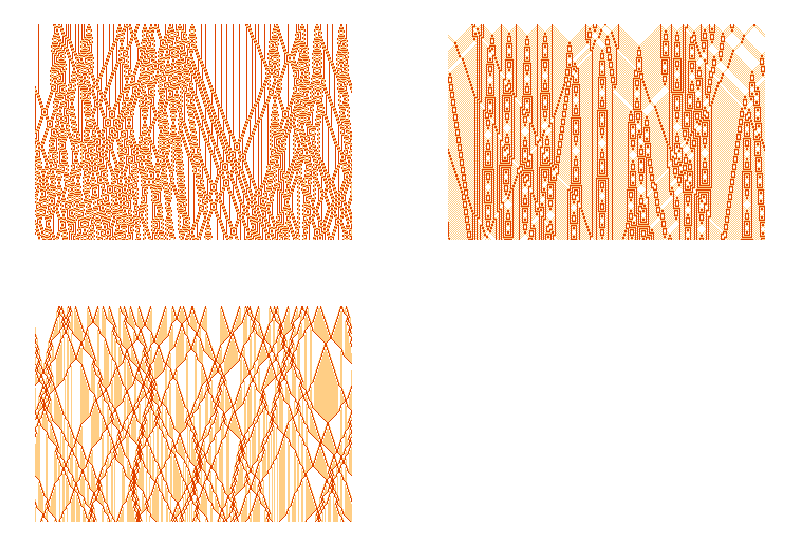

```mathematica
GraphicsGrid[Partition[MapThread[ArrayPlot[
Map[First,ResourceFunction["BlockCellularAutomaton"][{#,2},{#2,0},200]],
FrameStyle->GrayLevel[0.7],
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]
}]&,{{{{1,0}->{1,2},{0,1}->{2,1},{1,2}->{1,0},{2,1}->{0,1},{2,0}->{2,0},{0,2}->{0,2},{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},{{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},{2,1}->{2,0},{2,0}->{2,1},{0,2}->{1,2},{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},{{1,0}->{1,0},{0,1}->{0,1},{1,2}->{2,0},{2,1}->{0,2},{2,0}->{2,1},{0,2}->{1,2},{1,1}->{1,1},{0,0}->{0,0},{2,2}->{2,2}},{{1,0}->{2,0},{0,1}->{0,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,1},{0,2}->{1,0},{1,1}->{1,1},{0,0}->{0,0},{2,2}->{2,2}}},(SeedRandom[53535];RandomChoice[#->{2,0},300])&/@{{0.2,0.8},{0.05,0.95},{0.1,0.9},{0.25,0.75}}}],2]]
```

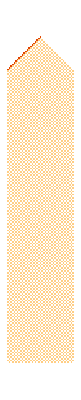
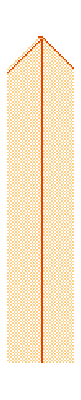
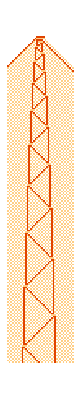
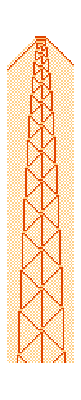
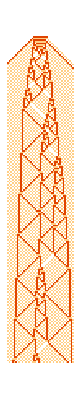
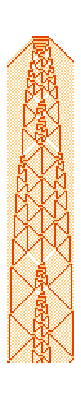

```mathematica
{{"[◼]", "CommaRow"}}[(ArrayPlot[#,
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]
},
FrameStyle->GrayLevel[0.7],
ImageSize->{Automatic,330}]&@(Take[First[#],{180,220}]&/@ResourceFunction["BlockCellularAutomaton"][{{
{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},2},
{CenterArray[#,400],0},200]))&/@Table[
Table[2,x],{x,1,11,2}],7]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

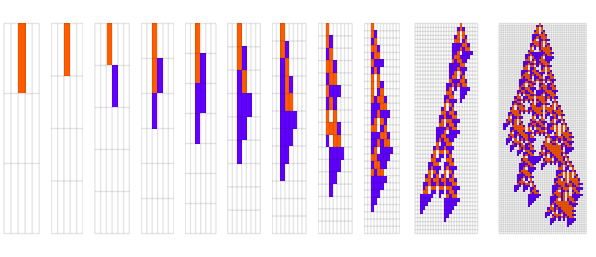

```mathematica
GraphicsRow[First/@res]
```

```mathematica
Row[ParallelMap[
Labeled[
Rasterize[Framed[First@WeaklyConnectedGraphComponents[{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#],96, ImageSize->{Automatic, 200}]],FrameStyle->Opacity[.3]], ImageSize->{Automatic, 150}],Text[Style[Column[{{{"[◼]", "Data"}}["$LifeData"][#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic,GrayLevel[0.25]]},Center],10,GrayLevel[0.25]]]]&,{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"}],Spacer[1]]
```

-Graphics-1991
(13 engines)-Graphics-1991
(10 engines)-Graphics-1993
(7 engines)-Graphics-1998
(6 engines)-Graphics-1998
(8 engines)-Graphics-2004
(3 engines)-Graphics-2005
(4 engines)-Graphics-2005
(5 engines)-Graphics-2017
(2 engines)

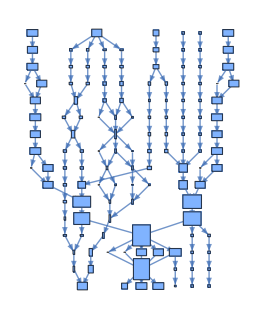
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Period-15 glider gun"],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&)],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Period-15 glider gun"]]},Spacer[20]]
```

The expectation is that biological life fundamentally makes use of certain “pockets of computational reducibility” that can be thought as associated with bulk orchestration.  If one can identify these, then one can effectively reduce them out for purposes of simulation, thereby dramatically increasing efficiency.  

Part of this project can potentially be done with very simple idealizations (such as cellular automata).  Another part to be explored has to do more realistically with the behavior of large molecules.  Once one no longer makes independent probabilistic model of interactions, one is dealing with what one can call “subchemistry”, in which one has to track individual molecules, and the causal relationships between their interactions. The formalism for things like this has been developed to some extent in the Wolfram Physics Project.  Here we would develop it further, and see how it informs bulk orchestration with actual molecules.

Per Nicholas Frieler’s WSS work, need more relevant pictures here I think

Another direction relates to the origin of bulk orchestration, which it may well be necessary to understand.  How do interactions between molecules build up things like autocatalytic sets that are relevant to the fundamental characteristics of life?  For this, we have methods based on multiway systems and other idealizations, together with idealized and not-so-idealized chemistry.  Early simulations show considerable promise, but have to be developed further, possibly using fairly large-scale computation.

## 2) Highly Idealized Models for Host-Pathogen Interactions and Evolution

#### Objective:

Develop foundational models that give strategic intuition about the space of possible viral threats, and support the development of practical strategies for threat neutralization and attribution

#### Background:

SW recently developed highly minimal models that (for the first time) seem to capture core features of biological evolution at the phenotypic level, i.e. with representations of the space of phenotypes and the way that different phenotypic structures can be produced.

Potential images here:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

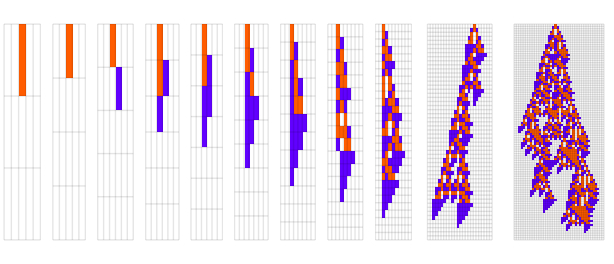

```mathematica
GraphicsRow[First/@res]
```

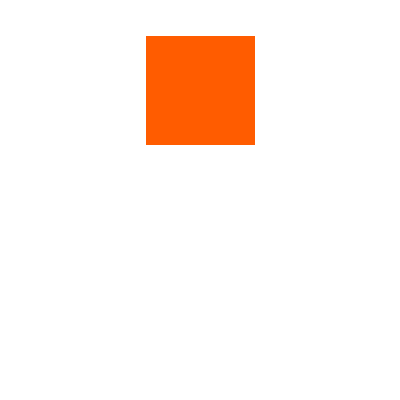
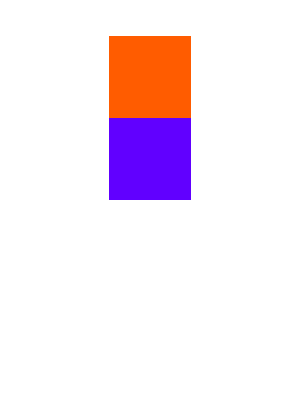
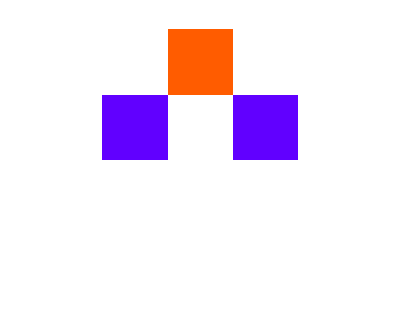
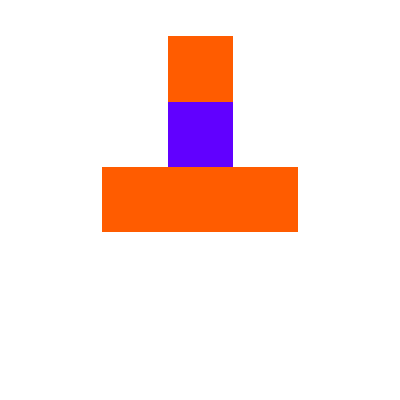
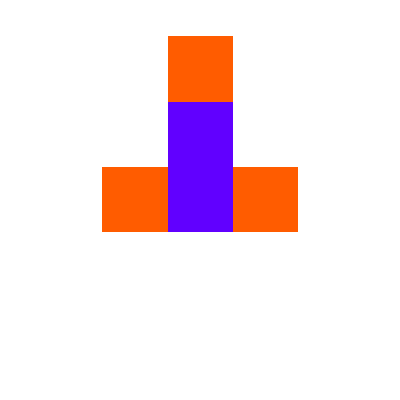
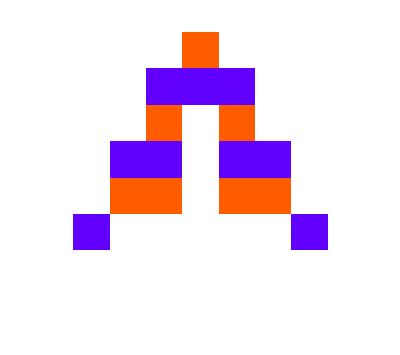
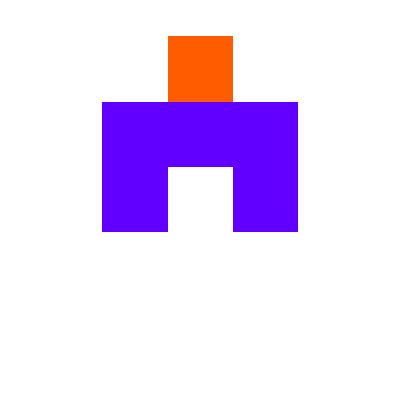
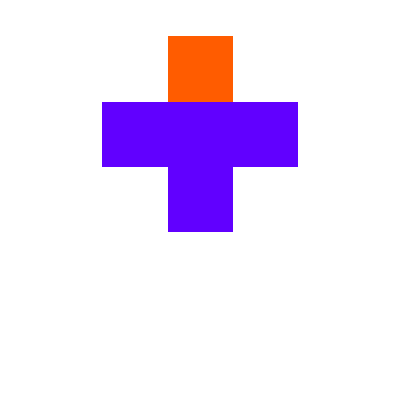
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
With[{init={1}},NestGraph[
{{"[◼]", "IterateMutations"}}[2,Greater,True][#,init,100]&,
{{{0,3,1},1}},4,VertexSize->2/4,EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",
VertexShapeFunction->Function[
Inset[ArrayPlot[ArrayPad[#,1]&/@
CellularAutomaton[#2[[1]],{init,0},#2[[2]]+1],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],#1,Automatic,
{Automatic,.8 Last[#3]Sqrt[ (#2[[2]]+2)]}
]],PerformanceGoal->"Quality"]]
```

```mathematica
{{"[◼]", "addVertexFigures"}}[VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
GraphLayout->"LayeredDigraphEmbedding",
"Reduced"->True,
AspectRatio->.7,
EdgeStyle->Directive[{Hue[0.6,0.4,0.5,.6]}]
],{{0,65815}}],{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},
"VertexFigures"->1,VertexSize->.3]
```

-Graphics-

These studies were done using particular sets of fitness functions.  The objective here would be to consider a much wider range of fitness functions, that idealize fitness functions encountered in viral etc. binding in biological systems.  Specifically, the initial approach would consist of investigating by enumerative simulation how easy or not it is to optimize different fitness functions.  

In SW’s original model, there is pure mutation.  We would want to generalize that to allow lateral gene transfer of the type seen in viruses, to find out how it affects what fitness functions can readily be evolved to.

We can think of the “viral” evolution as being evolution of a “key”.  We also need to study evolution of the “lock”, i.e. the organism (human, crop, etc.) into which the key is binding.  In other words, we want to study what fitness functions will be relevant.

Part of what will come out of this is an understanding of what structures can easily be “naturally evolved”, and what intermediates should occur in that evolution, versus what structures are more likely to have been produced by explicit engineering.

The basic studies envisaged here are idealized and computational.  But we anticipate that it will be possible to make contact with actual data on viruses, their binding sites, etc.  XXXX

## 3) [WN Version] Computation Foundations for the Engineered Versus Adapted Distinction

#### Objective

Use our recent foundational models to build a high-level computational framework for classifying engineered and adapted systems.

#### Background

Now that we have powerful minimal models for both adapted an engineered systems, it’s possible to formally observe the differences between these two types of system.

As mentioned above, one can look at the history of a system and determine whether its path follows that of an adapted system. But we’re beginning to see that even just looking at a snapshot of the system, it’s possible to observe certain characteristics that are suggestive of adapted or engineered design processes.

One important feature that we’ve already identified is the modularity of parts.

In our cellular automata models for biological evolution, the patterns that are found by adaptive search tend to have a high degree of interdependence between their parts, while the cellular automata that were constructed in the game of life consist of parts that each have their own function.

In using both qualitative and quantitative metrics for modularity, we’ve now begun to formalize the difference between engineered systems and adapted systems.

Despite major success with this approach, we’ve also found cases where measuring modularity is not sufficient for making the distinction.

Our goal therefore with this project would be twofold: First to further develop our ability to classify systems using metrics other than modularity, including more advanced machine learning methods. And secondly, to modify our current models to match more closely with the evolutionary behavior of viruses, allowing us to start to make classifications in practice.

## 3) [JKW version] Minimal models for classification and attribution of adaptive systems

#### Objective

Construct minimal, yet universal, theoretical methodologies that lets one look at an arbitrary adaptive system and tell, in some quantitative way, whether it is the product of unguided evolution or purposeful engineering.

#### Background

The Game of Life offers a multi-decade long “closed‑world” record of evolution: thousands of patterns whose origins are known, from hand‑built constructions to assemblies found only by automated search. Analysis of the two regimes shows differences in their multiway causal graphs. Engineered objects show shallow causal depth, obvious modular reuse and pockets of computational reducibility; search‑generated objects reach deeper into the computational wilderness, with heterogeneous motifs and little reuse.

These two regimes reduce to a handful of computable invariants: algorithmic‑complexity, causal‑graph depth, growth‑law exponents, etc. that act like reference frame through a multiway causal graph. We can apply the same analytic lens to viral genomes or synthetic gene circuits to find computationally reducible signatures; which could not only distinguish random evolutionary drift from purposeful construction, but might also carry stylistic, attributive fingerprints.

The approach would need to take into account the potential for threat actors to want to hide their tracks and make an engineered gene appear of natural origin. So we would want to pinpoint these features that an engineer cannot alter without destroying function, or look to determine if there is a kind compressibility gap between function and peripheral structure.

Similar to red-teaming exercises in software security, we can create adversarial scenarios to study the theoretical ability to both conceal and attribute features of these adaptive systems.